# Polygon

### Author

Eric W. Weisstein
August 3, 2010

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polygons/Polygon.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Polygon.html.

©2010 Wolfram Research, Inc. except for portions noted otherwise

## Figures

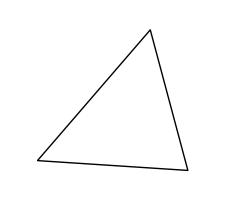
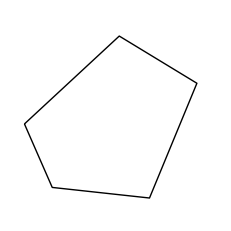
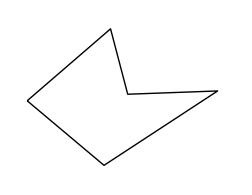
```mathematica
poly={-Graphics-,-Graphics-,-Graphics-};
```

### Broken Closed Line

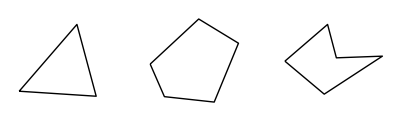

```mathematica
GraphicsGrid[{poly},ImageSize->400]
```

### Filled

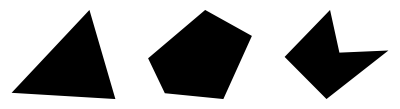

```mathematica
GraphicsGrid[{Graphics/@Polygon@@@poly[[All,1]]},ImageSize->400]
```

### Self-Intersecring

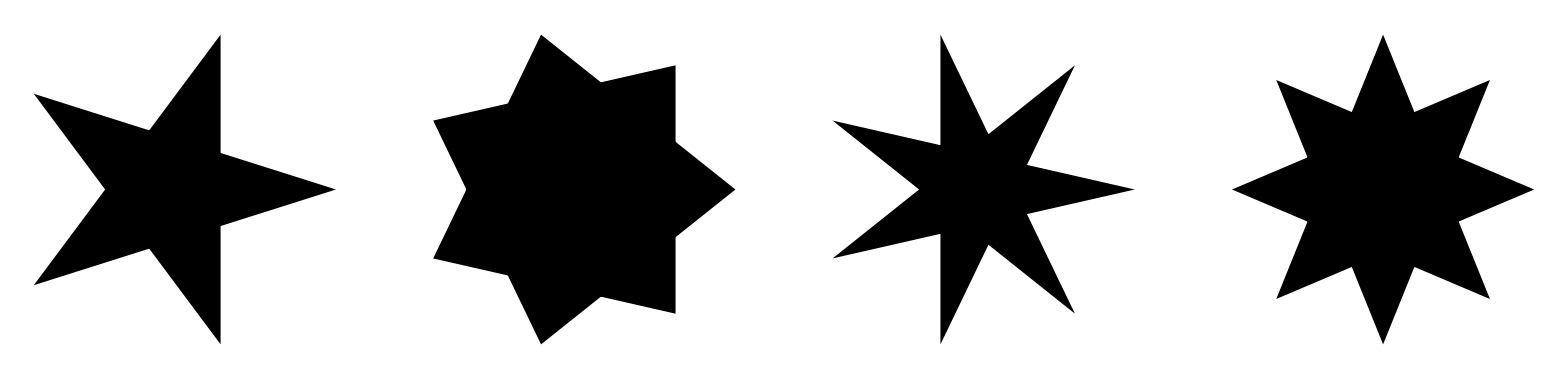

```mathematica
GraphicsGrid[{Graphics[Polygon[Most[#[[1,1]]]]]&/@(Polygram@@@{{5,2},{7,2},{7,3},{8,3}})}]
```

### All

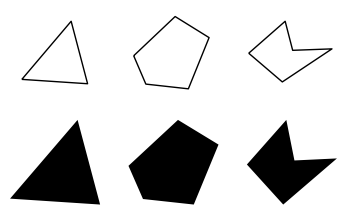

```mathematica
GraphicsGrid[{poly,Graphics/@Polygon@@@poly[[All,1]]}]
```